```mathematica
Log[(1/2)*(1+(Sin[t])^4+(Cos[t])^4)]
```

Log[1/2 (1+Cos[t]^4+Sin[t]^4)]

```mathematica
Simplify[Log[1/2 (1+Cos[t]^4+Sin[t]^4)]]
```

Log[1/8 (7+Cos[4 t])]

```mathematica
Simplify[Log[1+Cos[t]^4+Sin[t]^4]]
```

Log[1/4 (7+Cos[4 t])]

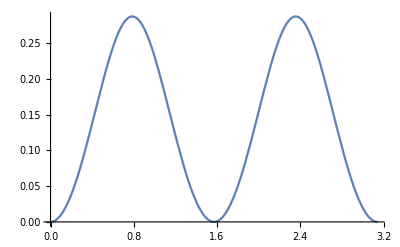

```mathematica
Plot[-Log[1/8 (7+Cos[4 t])],{t,0,Pi}]
```

```mathematica
Cos[a-b]//TrigExpand
```

Cos[a] Cos[b]+Sin[a] Sin[b]

```mathematica
pp=Table[{NN,-Sum[Log[2,1/8 (7+Cos[(2*Pi)/2^(NN-l)])],{l,1,NN}]},{NN,1,8}];
```

```mathematica
pp
```

{{1,0},{2,Log[4/3]/Log[2]},{3,Log[8/7]/Log[2]+Log[4/3]/Log[2]},{4,Log[8/7]/Log[2]+Log[4/3]/Log[2]-Log[1/8 (7+1/(√2))]/Log[2]},{5,Log[8/7]/Log[2]+Log[4/3]/Log[2]-Log[1/8 (7+1/(√2))]/Log[2]-Log[1/8 (7+Cos[π/8])]/Log[2]},{6,Log[8/7]/Log[2]+Log[4/3]/Log[2]-Log[1/8 (7+1/(√2))]/Log[2]-Log[1/8 (7+Cos[π/16])]/Log[2]-Log[1/8 (7+Cos[π/8])]/Log[2]},{7,Log[8/7]/Log[2]+Log[4/3]/Log[2]-Log[1/8 (7+1/(√2))]/Log[2]-Log[1/8 (7+Cos[π/32])]/Log[2]-Log[1/8 (7+Cos[π/16])]/Log[2]-Log[1/8 (7+Cos[π/8])]/Log[2]},{8,Log[8/7]/Log[2]+Log[4/3]/Log[2]-Log[1/8 (7+1/(√2))]/Log[2]-Log[1/8 (7+Cos[π/64])]/Log[2]-Log[1/8 (7+Cos[π/32])]/Log[2]-Log[1/8 (7+Cos[π/16])]/Log[2]-Log[1/8 (7+Cos[π/8])]/Log[2]}}

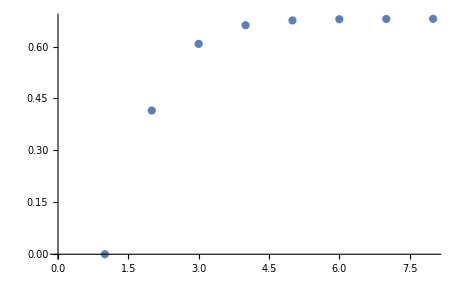

```mathematica
ListPlot[pp]
```

```mathematica
pp[[75]]//N
```

{75.,0.679914}

```mathematica
(-1/Pi)*Integrate[Log[2,1/8 (7+Cos[4*t])],{t,0,Pi}]//Simplify
```

Log[112-64 √3]/Log[2]

```mathematica
N[Log[112-64 √3]/Log[2]]
```

0.200063

```mathematica
3/7
```

3/7

```mathematica
N[3/7]
```

0.428571

```mathematica
Product[Cos[(Pi*)/d],{i,1,6}]
```

```mathematica
ll=Tuples[{0,1},6]
```

{{0,0,0,0,0,0},{0,0,0,0,0,1},{0,0,0,0,1,0},{0,0,0,0,1,1},{0,0,0,1,0,0},{0,0,0,1,0,1},{0,0,0,1,1,0},{0,0,0,1,1,1},{0,0,1,0,0,0},{0,0,1,0,0,1},{0,0,1,0,1,0},{0,0,1,0,1,1},{0,0,1,1,0,0},{0,0,1,1,0,1},{0,0,1,1,1,0},{0,0,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,0,1},{0,1,0,0,1,0},{0,1,0,0,1,1},{0,1,0,1,0,0},{0,1,0,1,0,1},{0,1,0,1,1,0},{0,1,0,1,1,1},{0,1,1,0,0,0},{0,1,1,0,0,1},{0,1,1,0,1,0},{0,1,1,0,1,1},{0,1,1,1,0,0},{0,1,1,1,0,1},{0,1,1,1,1,0},{0,1,1,1,1,1},{1,0,0,0,0,0},{1,0,0,0,0,1},{1,0,0,0,1,0},{1,0,0,0,1,1},{1,0,0,1,0,0},{1,0,0,1,0,1},{1,0,0,1,1,0},{1,0,0,1,1,1},{1,0,1,0,0,0},{1,0,1,0,0,1},{1,0,1,0,1,0},{1,0,1,0,1,1},{1,0,1,1,0,0},{1,0,1,1,0,1},{1,0,1,1,1,0},{1,0,1,1,1,1},{1,1,0,0,0,0},{1,1,0,0,0,1},{1,1,0,0,1,0},{1,1,0,0,1,1},{1,1,0,1,0,0},{1,1,0,1,0,1},{1,1,0,1,1,0},{1,1,0,1,1,1},{1,1,1,0,0,0},{1,1,1,0,0,1},{1,1,1,0,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,1,1,1,0,1},{1,1,1,1,1,0},{1,1,1,1,1,1}}

```mathematica
Length[ll]
```

4

```mathematica
ll[[2,2]]
```

1

```mathematica
Sum[Product[Cos[(Pi*(ll[[j1,i]]+ll[[j2,i]]+ll[[j3,i]]+ll[[j4,i]]))/d],{i,1,6}],{j1,1,Length[ll]},{j2,1,Length[ll]},{j3,1,Length[ll]},{j4,1,Length[ll]}]//Simplify
```

16777216 Cos[π/(2 d)]^24 Cos[(2 π)/d]^6

4096 Cos[π/(2 d)]^12 Cos[(2 π)/d]^3

```mathematica
2^24
```

16777216

```mathematica
-0.1250/10
```

-0.0125

```mathematica
-0.18/12
```

-0.015

```mathematica
0.3684/12
```

0.0307

```mathematica
0.43/14
```

0.0307143